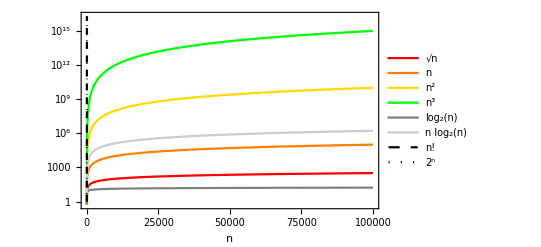

```mathematica
plot =LogPlot[{√n,n, n^2,n^3,Log[2,n],n Log[2,n],n!, 2^n},{n,0,10^5},
PlotRange->{0.5,2×10^16},
Frame->{True,True,False,False},FrameLabel->{"n",None},Axes->False,LabelStyle->{Black,15},
PlotStyle->{Red,Orange,Blend[{Yellow,Orange},0.3], Green,GrayLevel[0.5], GrayLevel[0.8], {Black,Dashed},{ Black,Dotted}},
PlotLegends->"Expressions"]
Export["/Users/jsaxon/Documents/Chicago/classes/lectures/img/fn.pdf",plot];
```